# Visualization of velocity distribution functions in 2D

## Equlibrium distributions

```mathematica
(*rho=5.0;ux = 0.2;uy = -0.1;*)
ClearAll[rho,ux,uy];

u[ux_,uy_]:= √(ux^2+uy^2);

w0[rho_]:= (2 rho)/9;w1[rho_] := rho/18;w2[rho_]:=rho/36;
```

#### Rest distribution (zero velocity)

```mathematica
feq0[ux_,uy_] := w0(2-3 u[ux,uy]^2);
```

#### Horizontal/vertical direction

```mathematica
feq1[rho_,ux_,uy_] := w1[rho](2+6ux+9 ux^2-3 u[ux,uy]^2);
feq3[rho_,ux_,uy_] := w1[rho](2+6uy+9 uy^2-3 u[ux,uy]^2);
feq5[rho_,ux_,uy_] := w1[rho](2-6ux+9 ux^2-3 u[ux,uy]^2);
feq7[rho_,ux_,uy_] := w1[rho](2-6uy+9 uy^2-3 u[ux,uy]^2);
```

#### Diagonal directions

```mathematica
feq2[rho_,ux_,uy_] := w2[rho](1+3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq4[rho_,ux_,uy_] := w2[rho](1-3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
feq6[rho_,ux_,uy_] := w2[rho](1-3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq8[rho_,ux_,uy_] := w2[rho](1+3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
```

```mathematica
scale = 1;
random=RandomReal[{1,2},8];
feq[rho_,ux_,uy_] :=Map[Apply[#,{rho,ux,uy}]&, {feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8}];
a1 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,0}}]}];
a2 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,1}}]}];
a3 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,1}}]}];
a4 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,1}}]}];
a5 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,0}}]}];
a6 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,-1}}]}];
a7 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,-1}}]}];
a8 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,-1}}]}];
factor = ({Cos@#,Sin@#}&/@Range[0,7 Pi/4,Pi/4]);

Manipulate[
(*With[{rho=5,ux=0,uy=0},*)
data = feq[rho,ux,uy]*random;

data2=factor* data;
AppendTo[data2,data2[[1]]];
f=BSplineFunction[data2,SplineDegree->1];

g2=ParametricPlot[(r f[t]),{t,0,1},{r,0,1},BoundaryStyle->{Thick,Black},Frame->True,PlotRangePadding->.2,PlotRange->scale, MeshFunctions->(#3&),Mesh->(Length[data2]-2),MeshShading->{LightRed},Axes->False,Ticks->None,AxesStyle->None, FrameTicks->Automatic];

Show[g2,a1, a2, a3, a4, a5, a6, a7, a8]
(*]*),{{rho,2.5}, 0,5},{{ux,0},0,√(1/3)},{{uy,0},0,√(1/3)}]
```

# Visualization of velocity distribution functions in 2D

## Equlibrium distributions

```mathematica
(*rho=5.0;ux = 0.2;uy = -0.1;*)
ClearAll[rho,ux,uy,precalc];

u[ux_,uy_]:= √(ux^2+uy^2);

w0[rho_]:= (2 rho)/9;
w1[rho_] := rho/18;
w2[rho_]:=rho/36;
usqr[ux_,uy_] :=(ux^2+uy^2);
```

#### Pre calculations

```mathematica
precalc[rho_,ux_,uy_]:=(
weight1 = w1[rho];
weight2 = w2[rho];
uxSquare = ux^2;
uySquare = uy^2;
uSquare = uxSquare +uySquare;
uxuy = ux uy;
)
```

#### Horizontal/vertical direction

```mathematica
calcFeqHorizontalVertical[ux_,uy_] :=
(feq1= weight1(2+6ux+9uxSquare-3uSquare);
feq3= weight1(2+6uy+9uySquare-3uSquare);
feq5= weight1(2-6ux+9uxSquare-3uSquare);
feq7= weight1(2-6uy+9uySquare-3uSquare);
)
```

#### Diagonal directions

```mathematica
calcFeqDiagonal[ux_,uy_]:=
(feq2= weight2(1+3(ux+uy)+9uxuy + 3uSquare);
feq4= weight2(1-3(ux-uy)-9uxuy + 3uSquare);
feq6= weight2(1-3(ux+uy)+9uxuy + 3uSquare);
feq8= weight2(1+3(ux-uy)-9uxuy + 3uSquare);
)
```

```mathematica
With[{rho=5,ux=0,uy=0},
precalc[rho,ux,uy];
weight1
]
```

```mathematica
ClearAll[weight1, weight2,uxSquare,uySquare,uSquare,uxuy,feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8];
```

```mathematica
weight2
```

```mathematica
calcFeqHorizontalVertical[1,2]
```

```mathematica
calcFeqDiagonal[1,2]
```

```mathematica
ClearAll[weight1, weight2,uxSquare,uySquare,uSquare,uxuy,feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8];
scale = 1;
random=RandomReal[{1,2},8];
(*feq[rho_,ux_,uy_] :=Map[Apply[#,{rho,ux,uy}]&, {feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8}];*)
a1 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,0}}]}];
a2 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,1}}]}];
a3 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,1}}]}];
a4 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,1}}]}];
a5 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,0}}]}];
a6 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,-1}}]}];
a7 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,-1}}]}];
a8 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,-1}}]}];
factor = ({Cos@#,Sin@#}&/@Range[0,7 Pi/4,Pi/4]);

Manipulate[
(*With[{rho=5,ux=0,uy=0},*)
precalc[rho,ux,uy];
calcFeqHorizontalVertical[ux,uy];
calcFeqDiagonal[ux,uy];
data = {feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8}*random;

data2=factor* data;
AppendTo[data2,data2[[1]]];
f=BSplineFunction[data2,SplineDegree->1];

g2=ParametricPlot[(r f[t]),{t,0,1},{r,0,1},BoundaryStyle->{Thick,Black},Frame->True,PlotRangePadding->.2,PlotRange->scale, MeshFunctions->(#3&),Mesh->(Length[data2]-2),MeshShading->{LightRed},Axes->False,Ticks->None,AxesStyle->None, FrameTicks->Automatic];

Show[g2,a1, a2, a3, a4, a5, a6, a7, a8]
(*]*),{{rho,2.5}, 0,5},{{ux,0},0,√(1/3)},{{uy,0},0,√(1/3)}]
```

```mathematica
ClearAll[weight1, weight2,uxSquare,uySquare,uSquare,uxuy,feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8];
```

#### Rest distribution (zero velocity)

```mathematica
feq0[ux_,uy_] := w0(2-3 u[ux,uy]^2);
```

#### Horizontal/vertical direction

```mathematica
feq1[rho_,ux_,uy_] := w1[rho](2+6ux+9 ux^2-3 u[ux,uy]^2);
feq3[rho_,ux_,uy_] := w1[rho](2+6uy+9 uy^2-3 u[ux,uy]^2);
feq5[rho_,ux_,uy_] := w1[rho](2-6ux+9 ux^2-3 u[ux,uy]^2);
feq7[rho_,ux_,uy_] := w1[rho](2-6uy+9 uy^2-3 u[ux,uy]^2);
```

#### Diagonal directions

```mathematica
feq2[rho_,ux_,uy_] := w2[rho](1+3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq4[rho_,ux_,uy_] := w2[rho](1-3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
feq6[rho_,ux_,uy_] := w2[rho](1-3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq8[rho_,ux_,uy_] := w2[rho](1+3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
```

```mathematica
scale = 1;
random=RandomReal[{1,2},8];
feq[rho_,ux_,uy_] :=Map[Apply[#,{rho,ux,uy}]&, {feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8}];
a1 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,0}}]}];
a2 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,1}}]}];
a3 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,1}}]}];
a4 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,1}}]}];
a5 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,0}}]}];
a6 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,-1}}]}];
a7 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,-1}}]}];
a8 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,-1}}]}];
factor = ({Cos@#,Sin@#}&/@Range[0,7 Pi/4,Pi/4]);

Manipulate[
(*With[{rho=5,ux=0,uy=0},*)
data = feq[rho,ux,uy]*random;

data2=factor* data;
AppendTo[data2,data2[[1]]];
f=BSplineFunction[data2,SplineDegree->1];

g2=ParametricPlot[(r f[t]),{t,0,1},{r,0,1},BoundaryStyle->{Thick,Black},Frame->True,PlotRangePadding->.2,PlotRange->scale, MeshFunctions->(#3&),Mesh->(Length[data2]-2),MeshShading->{LightRed},Axes->False,Ticks->None,AxesStyle->None, FrameTicks->Automatic];

Show[g2,a1, a2, a3, a4, a5, a6, a7, a8]
(*]*),{{rho,2.5}, 0,5},{{ux,0},0,√(1/3)},{{uy,0},0,√(1/3)}]
```

```mathematica
feq[5,0,0]
```

```mathematica
ClearAll[rho,ux,uy,g2,f,data,data2,random];
scale = 1;
random=RandomReal[{1,2},8];
feq[rho_,ux_,uy_] :=Map[Apply[#,{rho,ux,uy}]&, {feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8}];
a1 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,0}}]}];
a2 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,1}}]}];
a3 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,1}}]}];
a4 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,1}}]}];
a5 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,0}}]}];
a6 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{-1,-1}}]}];
a7 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{0,-1}}]}];
a8 =Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*{1,-1}}]}];
factor = ({Cos@#,Sin@#}&/@Range[0,7 Pi/4,Pi/4]);


generateFeqPlot[rho_,ux_,uy_]:=Module[{f,g2},

data = feq[rho,ux,uy];
data2=factor* data;
AppendTo[data2,data2[[1]]];
     f=BSplineFunction[data2,SplineDegree->1];

g2=ParametricPlot[(r f[t]),{t,0,1},{r,0,1},BoundaryStyle->{Thick,Black},Frame->True,PlotRangePadding->.2,PlotRange->scale, MeshFunctions->(#3&),Mesh->(Length[data2]-2),MeshShading->{LightRed},Axes->False,Ticks->None,AxesStyle->None, FrameTicks->None];
g2

]


p1=generateFeqPlot[5,0,0];
p2=generateFeqPlot[5,0,0];
{Show[p1,a1, a2, a3, a4, a5, a6, a7, a8],Show[p2,a1, a2, a3, a4, a5, a6, a7, a8]}
```

```mathematica
Table[Table[Show[p1,a1, a2, a3, a4, a5, a6, a7, a8],3],3];
```

```mathematica
Table[Table[Show[generateFeqPlot[RandomReal[{3,5}],RandomReal[{0,0.2*√(1/3)}],RandomReal[{0,0.2*√(1/3)}]],a1, a2, a3, a4, a5, a6, a7, a8],3],3]
```

```mathematica
data
```

# Visualize output from c++ code

```mathematica
ClearAll[scale,scale2,thickness,arrowCollor,rho,ux,uy,g2,f,data,data2,random];
scale = 0.1;
```

Directions

```mathematica
makeArrows[]:=(
scale2 = 3;
thickness = 0.001;
arrowCollor = LightGray;
a1 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{1,0}}]}];
a2 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{1,1}}]}];
a3 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{0,1}}]}];
a4 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{-1,1}}]}];
a5 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{-1,0}}]}];
a6 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{-1,-1}}]}];
a7 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{0,-1}}]}];
a8 =Graphics[{Thickness[thickness],arrowCollor,Arrow[{{0,0}, scale2*scale*{1,-1}}]}];
)
```

```mathematica
populationArrows[{1,1,1,1,1,1,1,1}];
```

```mathematica
?
```

Populations

```mathematica
factor = ({Cos@#,Sin@#}&/@Range[0,7 Pi/4,Pi/4]);

plotPolulations[populations_]:=Module[{populations2, f,plot},
populations2=factor* populations;
AppendTo[populations2,populations2[[1]]];
     f=BSplineFunction[populations2,SplineDegree->1];

plot=ParametricPlot[(r f[t]),{t,0,1},{r,0,1},BoundaryStyle->{Thick,Black},Frame->True,PlotRangePadding->.2,PlotRange->scale, MeshFunctions->(#3&),Mesh->(Length[populations2]-2),MeshShading->{LightRed},Axes->False,Ticks->None,AxesStyle->None, FrameTicks->None];
plot
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
filename="testfile"<>".txt";
populationList = If[FileExistsQ[filename],Get[filename]];
populationList[[4,2;;-2,2;;-2,;;-2]]//MatrixForm;
```

```mathematica
makeArrows[];
```

```mathematica
populationsView =Map[Map[Show[plotPolulations[#],a1, a2, a3, a4, a5, a6, a7, a8]&, #[[2;;-2,2;;-2,;;-2]],{2}]&,populationList[[All]]];
```

```mathematica
ListAnimate[MatrixForm/@populationsView,AnimationRunning->False]
```

```mathematica
subList = populationList[[All,2;;-2,2;;-2,;;-2]];
```

```mathematica
populationArrows[populations_]:=Module[{scale2,thickness,arrowCollor,directions,scaledDirections,populationScaledDirections,pArrows,pThickness},
scale2 = 1;
thickness = 1;
arrowCollor = Red;
directions = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};

scaledDirections = #/If[Plus@@(#^2)>0,√(Plus@@(#^2)),1]&/@directions;
(*scaledDirections = directions;*)
populationScaledDirections = scaledDirections * populations;
pArrows = (Arrow[{{0,0},(scale2*#)/1}]&/@populationScaledDirections)[[All]];
Graphicss[{Thickness[thickness],arrowCollor,pArrows}];
pArrows = (Arrow[{{0,0},(scale2*#)/If[Plus@@(#^2)>0,√(Plus@@(#^2)),1]}]&/@directions)[[All]];
pThickness = Thickness/@(thickness*populations^2);

Graphicss@Flatten@Transpose@{Table[arrowCollor,8],pThickness,pArrows}
];
Map[populationArrows,subList,{3}][[1,2]]//MatrixForm
```

(Graphicss[{RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{1,0}}],RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{0,1}}],RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{-1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{-1,0}}],RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{-1/(√2),-1/(√2)}}],RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{0,-1}}],RGBColor[1, 0, 0],Thickness[1.44],Arrow[{{0,0},{1/(√2),-1/(√2)}}]}]
Graphicss[{RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{1,0}}],RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{0,1}}],RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{-1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{-1,0}}],RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{-1/(√2),-1/(√2)}}],RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{0,-1}}],RGBColor[1, 0, 0],Thickness[4.84],Arrow[{{0,0},{1/(√2),-1/(√2)}}]}]
Graphicss[{RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{1,0}}],RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{0,1}}],RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{-1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{-1,0}}],RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{-1/(√2),-1/(√2)}}],RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{0,-1}}],RGBColor[1, 0, 0],Thickness[10.24],Arrow[{{0,0},{1/(√2),-1/(√2)}}]}]
Graphicss[{RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{1,0}}],RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{0,1}}],RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{-1/(√2),1/(√2)}}],RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{-1,0}}],RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{-1/(√2),-1/(√2)}}],RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{0,-1}}],RGBColor[1, 0, 0],Thickness[17.64],Arrow[{{0,0},{1/(√2),-1/(√2)}}]}])

```mathematica
({{Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642012167799917,-0.019642012167799917}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642012167799917,-0.019642012167799917}}]}}]}, {Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.191111,0.}}],Arrow[{{0,0},{0.03378414779153086,0.03378414779153086}}],Arrow[{{0,0},{0.,0.104444}}],Arrow[{{0,0},{-0.010213450347458491,0.010213450347458491}}],Arrow[{{0,0},{-0.057778,0.}}],Arrow[{{0,0},{-0.010213450347458491,-0.010213450347458491}}],Arrow[{{0,0},{0.,-0.104444}}],Arrow[{{0,0},{0.03378414779153086,-0.03378414779153086}}]}}]}, {Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642012167799917,-0.019642012167799917}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642012167799917,-0.019642012167799917}}]}}]}, {Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642012167799917,-0.019642012167799917}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642012167799917,-0.019642012167799917}}]}}]}, {Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642012167799917,-0.019642012167799917}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642012167799917,-0.019642012167799917}}]}}]}, {Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642012167799917,-0.019642012167799917}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642012167799917,-0.019642012167799917}}]}}]}})
```

{Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642,0.019642}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642,0.019642}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642,-0.019642}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642,-0.019642}}]}}],Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.191111,0.}}],Arrow[{{0,0},{0.0337841,0.0337841}}],Arrow[{{0,0},{0.,0.104444}}],Arrow[{{0,0},{-0.0102135,0.0102135}}],Arrow[{{0,0},{-0.057778,0.}}],Arrow[{{0,0},{-0.0102135,-0.0102135}}],Arrow[{{0,0},{0.,-0.104444}}],Arrow[{{0,0},{0.0337841,-0.0337841}}]}}],Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642,0.019642}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642,0.019642}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642,-0.019642}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642,-0.019642}}]}}],Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642,0.019642}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642,0.019642}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642,-0.019642}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642,-0.019642}}]}}],Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642,0.019642}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642,0.019642}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642,-0.019642}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642,-0.019642}}]}}],Graphicss[{Thickness[0.01],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642,0.019642}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642,0.019642}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642,-0.019642}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642,-0.019642}}]}}]}

```mathematica
Graphicss[{Thickness[0.05],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642012167799917,0.019642012167799917}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642012167799917,-0.019642012167799917}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642012167799917,-0.019642012167799917}}]}}]
```

Graphicss[{Thickness[0.05],RGBColor[1, 0, 0],{Arrow[{{0,0},{0.111111,0.}}],Arrow[{{0,0},{0.019642,0.019642}}],Arrow[{{0,0},{0.,0.111111}}],Arrow[{{0,0},{-0.019642,0.019642}}],Arrow[{{0,0},{-0.111111,0.}}],Arrow[{{0,0},{-0.019642,-0.019642}}],Arrow[{{0,0},{0.,-0.111111}}],Arrow[{{0,0},{0.019642,-0.019642}}]}}]

```mathematica
{Graphicss[{Arrow[{{0,0},{1,0}}],Thickness[0.00555555],RGBColor[1, 0, 0]}],Graphicss[{Arrow[{{0,0},{1/(√2),1/(√2)}}],Thickness[0.0013889000000000002],RGBColor[1, 0, 0]}],Graphicss[{Arrow[{{0,0},{0,1}
}],Thickness[0.00555555],RGBColor[1, 0, 0]}],Graphicss[{Arrow[{{0,0},{-1/(√2),1/(√2)}}],Thickness[0.0013889000000000002],RGBColor[1, 0, 0]}],Graphicss[{Arrow[{{0,0},{-1,0}}],Thickness[0.00555555],RGBColor[1, 0, 0]}],Graphicss[{Arrow[{{0,0},{-1/(√2),-1/(√2)}}],Thickness[0.0013889000000000002],RGBColor[1, 0, 0]}],Graphicss[{Arrow[{{0,0},{0,-1}}],Thickness[0.00555555],RGBColor[1, 0, 0]}],Graphicss[{Arrow[{{0,0},{1/(√2),-1/(√2)}}],Thickness[0.0013889000000000002],RGBColor[1, 0, 0]}]}
```

```mathematica
MatrixForm/@Map[populationArrows,subList,{3}];
```

```mathematica
ListAnimate[MatrixForm/@Map[populationArrows,subList,{3}],AnimationRunning->False]
```

```mathematica
SetDirectory[NotebookDirectory[]];
filename="population"<>".txt";
populationList = If[FileExistsQ[filename],Get[filename]];
populationList[[4,2;;-2,2;;-2,;;-2]]//MatrixForm;
subList = populationList[[All,2;;-2,2;;-2,;;-2]];
```

```mathematica
ClearAll[filename,populationList, subList,populationArrows];
populationArrows[populations_]:=Module[{scale2,thickness,arrowCollor,directions,scaledDirections,populationScaledDirections,pArrows,pThickness,pCollor},
scale2 = 1;
thickness = 200;
arrowCollor = Red;
directions = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};
pArrows = (Arrow[{{0,0},(scale2*#)/If[Plus@@(#^2)>0,√(Plus@@(#^2)),1]}]&/@directions);
pThickness = AbsoluteThickness/@(thickness*populations^2);
pCollor = Table[arrowCollor,Length@directions];
(*first = List[Flatten@Transpose@{pCollor,pThickness,pArrows},ImageSize->Tiny];*)
(*Join[{Apply[List,Map[{#}&,pCollor+pThickness+pArrows],{2}]},{ImageSize->Tiny}]*)
(*Sequence@@{Transpose[{pCollor,pThickness,pArrows}],ImageSize->Tiny};*)

Graphics@(Sequence@@{Transpose[{pCollor,pThickness,pArrows}],ImageSize->Tiny})

];

SetDirectory[NotebookDirectory[]];
filename="population"<>".txt";
populationList = If[FileExistsQ[filename],Get[filename]];

(*populationList[[4,2;;-2,2;;-2,;;-2]]//MatrixForm;*)
subList = populationList[[All,2;;-2,2;;-2,;;-2]];
subList//MatrixForm;
populationArrows[subList[[1,1,1]]];
Map[populationArrows,subList,{3}][[1,2]]//MatrixForm;
Map[populationArrowss,subList,{3}];
Map[populationArrows,subList,{3}]//MatrixForm;
ListAnimate[MatrixForm/@Map[populationArrows,subList,{3}],AnimationRunning->False]
```

## Velocity plots

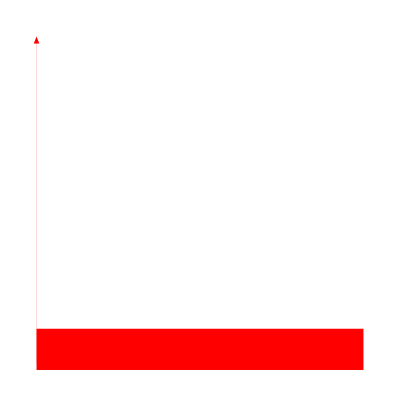

```mathematica
ClearAll[filename,populationList, subList,populationArrows];
velocityArrows[velocities_]:=Module[{scale2,thickness,arrowCollor,directions,scaledDirections,populationScaledDirections,pArrows,pThickness,pCollor},
scale2 = 1;
thickness = 100;
arrowCollor = Red;
directions = {{1,0},{0,1}};
pArrows = (Arrow[{{0,0},#}]&/@directions);
pThickness = AbsoluteThickness/@(thickness*velocities);
pCollor = Table[arrowCollor,Length@directions];
(*first = List[Flatten@Transpose@{pCollor,pThickness,pArrows},ImageSize->Tiny];*)
(*Join[{Apply[List,Map[{#}&,pCollor+pThickness+pArrows],{2}]},{ImageSize->Tiny}]*)
(*Sequence@@{Transpose[{pCollor,pThickness,pArrows}],ImageSize->Tiny};*)

Graphics@(Sequence@@{Transpose[{pCollor,pThickness,pArrows}],ImageSize->Tiny})

];
velocityArrows[{1.,0.}]
```

```mathematica
ClearAll[filename,velocityList,subVelocityList];
SetDirectory[NotebookDirectory[]];
filename="velocity"<>".txt";
velocityList = If[FileExistsQ[filename],Get[filename]];
subVelocityList = velocityList[[All,2;;-2,2;;-2]];
```

```mathematica
ListAnimate[MatrixForm/@Map[velocityArrows,subVelocityList,{3}],AnimationRunning->False]
```